```mathematica
f1[u_]:={Sin[u],Cos[u]}
f2[u_]:={(5-0.2 u) Sin[u],Cos[u]}
```

```mathematica
Manipulate[ParametricPlot3D[Append[v*f1[u]+(1-v) f2[u],v],{u,0,umax},{v,0,vmax},BoxRatios->{1,1,1}, AxesLabel->Automatic], {umax, 0.1, 2*Pi}, {vmax, 0.1, 1}]
```

```mathematica
f0102[u_]:= {u*20*((3)^(1/2))/(300*(19)^(1/2)), (1/80)*(u*20*(30)^(1/2)/(300*(19)^(1/2)))^2}
f0201[u_]:= {u*5*((57)^(1/2))/(300*(19)^(1/2)), (1/95)*(u*5*(570)^(1/2)/(300*(19)^(1/2)))^2}
```

```mathematica
ParametricPlot3D[Append[v*f0102[u]+(10-v) f0201[u],v],{u,-30*(19)^(1/2),30*(19)^(1/2)},{v,0,10},BoxRatios->{1,1,1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Clear[sweptParabola]
sweptParabola[f1_, f2_]:= Append[v*f2[u]+(10-v) f1[u],v]
surf0102 = sweptParabola[f0102, f0201]
reg0102 = ImplicitRegion[{x,y,z}∈ParametricRegion[{surf0102[[1]], surf0102[[2]]+w, surf0102[[3]]}, {{u, -30*(19)^(1/2),30*(19)^(1/2)},{ v, 0, 10}, {w,0,15}}], {{x,-300*(19)^(1/2),300*(19)^(1/2)}, {y, 0, 15}, {z, 0, 10}}]
RegionPlot3D[{x,y,z}∈reg0102,{x,-40,40}, {y, 0, 15}, {z, 0, 10}]
```

{(u (10-v))/(5 √57)+(u v)/(20 √3),(u^2 (10-v))/11400+(u^2 v)/11400,v}

ImplicitRegion[{x,y,z}∈ParametricRegion[{{(u (10-v))/(5 √57)+(u v)/(20 √3),(u^2 (10-v))/11400+(u^2 v)/11400+w,v},-30 √19≤u≤30 √19&&0≤v≤10&&0≤w≤15},{u,v,w}]&&-300 √19≤x≤300 √19&&0≤y≤15&&0≤z≤10,{x,y,z}]

-Graphics3D-

ImplicitRegion[x≤40&&x≥-40&&z≥0&&z≤10&&y≤15&&y≥15 x^2 (1-z)+15 x^2 z,{x,y,z}]

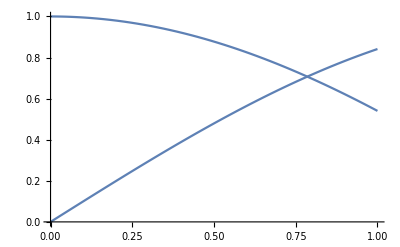

```mathematica
ImplicitRegion[x≤40&&x≥-40&&z≥0&&z≤10&& y≤15&&y≥15 x^2 (1-z)+15 x^2 z,{x,y,z}]
```